# VYA - Přednášky

## 8. Přednáška

### Komplexní čísla

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
z = 3 + 4I
```

3+4 ⅈ

```mathematica
?I
```

```mathematica
{z, Re[z], Im[z], Abs[z], √(Re[z]^2+ Im[z]^2), Arg[z]}
```

{3+4 ⅈ,3,4,5,5,ArcTan[4/3]}

```mathematica
Arg /@ {0, I, -1, -I}
```

{0,π/2,π,-π/2}

```mathematica
?Arg
```

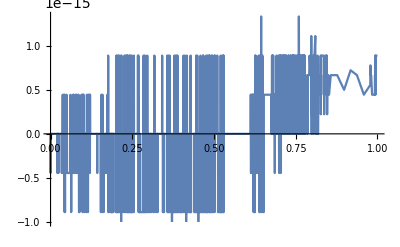

```mathematica
U1[t_] := 5*Sin[3t + 0.4]
U2[t_] := Im[5 * Exp[I * 0.4] * Exp[I * 3 * t]]
Plot[U1[t] - U2[t], {t, 0, 1}]
```

```mathematica
Sin[psi + Pi/2]
```

Cos[psi]

```mathematica
Sin'
```

Cos[#1]&

```mathematica
{Abs[I], Arg[I]}
```

{1,π/2}

### Chování RLC v HUS

R: u_R(t) = R*I_R(t) 
	U_R = R*I_R
L: u_L(t) = L*dI_L/dt
	U_L = L*j*ω*I
C: I_c(t) = C*dU_c/dt
	I_C = C*j*ω*U_C
U_C = 1/(j*ω*C)*I_C

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
L = 33 mH;
mH = 10^-3;
IL[t_] := 10^-3*Sin[1000t +0.123]
UL[t_] := L * IL'[t]
```

```mathematica
ILFaz = 0.001 * E^(I*0.123);
Print["ILFazor = ", ILFaz, " A"]
```

ILFazor = 0.000992445+0.00012269 ⅈ A

```mathematica
ω = 1000;
ULFaz = I * ω * L * ILFaz;
Print["ULFazor = ", ULFaz, " V"]
```

ULFazor = -0.00404877+0.0327507 ⅈ V

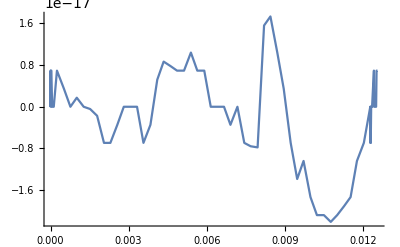

```mathematica
ULtFaz[t_] := Im[ULFaz * E^(I*ω*t)] 
T = (2Pi)/ω;
Plot[UL[t] - ULtFaz[t], {t,0,2T}]
```

```mathematica
{Arg[ILFaz], Arg[ULFaz]}
```

{0.123,1.6938}

```mathematica
(Arg[ILFaz] - Arg[ULFaz])/Pi
```

-0.5

### Vypočítaný obvod

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
Uz = 10*Sin[cos[t] + 0.123]
Um = 10.;
fi = 0.123;
ω = 1000;
T = (2Pi)/ω;
UzFaz = Um * E^(I*ω)
```

10 Sin[0.123+cos[t]]

5.62379+8.2688 ⅈ

```mathematica
Rovn = {
Iuz == IR1 + IC,
IR1 + IC == IR2 + IL,

U1 == R2 * IR2,
U1 ==  I * ω * L * IL,
UzFaz - U1 == R1 * IR1,
UzFaz - U1 == 1/(I * ω * Cl)* IC
}
```

{Iuz==IC+IR1,IC+IR1==IL+IR2,U1==200 IR2,U1==33 ⅈ IL,(5.62379+8.2688 ⅈ)-U1==100 IR1,(5.62379+8.2688 ⅈ)-U1==(0.-212.766 ⅈ) IC}

```mathematica
Neznam =Union[Cases[Rovn, _Symbol, {0, ∞}]]
```

{IC,IL,IR1,IR2,Iuz,U1}

```mathematica
Length /@ {Rovn, Neznam}
```

{6,6}

```mathematica
Res = Solve[Rovn][[1]]
```

{IC→-0.027752+0.0399534 ⅈ,IL→0.0716398+0.0871796 ⅈ,IR1→0.0850072+0.0590468 ⅈ,IR2→-0.0143846+0.0118206 ⅈ,Iuz→0.0572552+0.0990002 ⅈ,U1→-2.87693+2.36411 ⅈ}

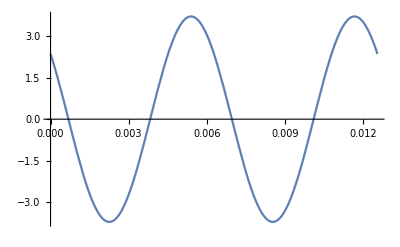

```mathematica
U1[t_] := Im[(U1 /. Res) * E^(I*ω*t)]
Plot[U1[t], {t, 0, 2T}]
```

```mathematica
U1 /. Res
Print["Amplituda U1 = ", Abs[U1 /. Res], " V"]
Print["Počáteční fáze U1 = ", Arg[U1 /. Res], " Rad"]
```

-2.87693+2.36411 ⅈ

Amplituda U1 = 3.72367 V

Počáteční fáze U1 = 2.45373 Rad

### Zvuk

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Play[Sin[440 * 2Pi t], {t, 0, 1}]
```

-Graphics-

```mathematica
Play[{Sin[440 * 2Pi t], Sin[360 * 2Pi t]}, {t, 0, 1}]
```

-Graphics-